# Functional form harvest output vs preciptation

```mathematica
ClearAll[x,a,b,y,sigma, rho, theta]
```

## Coefficient functions

#### Coefficient “a”

```mathematica
ClearAll[L,x0,k,a,b,y, x]
```

```mathematica
sigma = {8.76366499, -1.340874, -1.565776}
```

{8.76366,-1.34087,-1.56578}

```mathematica
rho = {-0.01630416,96.716459, 87.058386, 70}
```

{-0.0163042,96.7165,87.0584,70}

```mathematica
theta = {2.064378}
```

{2.06438}

```mathematica
a = sigma[[1]]*x *Exp[rho[[1]]*x]
```

8.76366 ⅇ^(-0.0163042 x) x

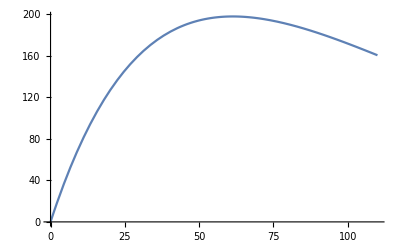

```mathematica
Plot[a,{x,0, 110}]
```

#### Coefficient “b”

```mathematica
b = sigma[[2]]+rho[[2]]*x^theta[[1]]
```

-1.34087+96.7165 x^2.06438

```mathematica
b=sigma[[2]] + (x/rho[[2]])^theta
```

{-1.34087+0.0000796483 x^2.06438}

```mathematica
b= sigma[[3]] + x/rho[[2]]
```

-1.56578+0.0103395 x

```mathematica
b /. x ->0
```

-1.56578

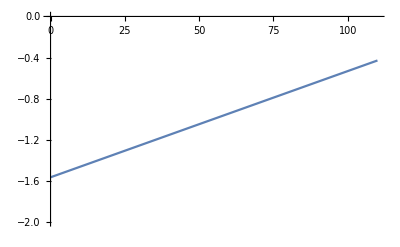

```mathematica
Plot[b,{x,0,110}, PlotRange-> {{0,110},{-2,0}}]
```

#### Where z is precipitation

## Harvest Output function

```mathematica
y = a z Exp[b z]
```

8.76366 ⅇ^(-0.0163042 x+(-1.56578+0.0103395 x) z) x z

```mathematica
Plot3D[y,{x,0,110},{z,0,2}, AxesLabel->{"Yield Mean","LSU"}, ColorFunction-> ColorData["AvocadoColors"]]
```

-Graphics3D-

#### Where x is LSU

## Plotting harvest output vs precipitation

-Graphics3D-